# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["/Users/pcs/Desktop/Quantum channel/QMB_offline.wl"];
```

```mathematica
LaunchKernels[10]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[]]+I RandomVariate[NormalDistribution[]],{2^L}]];
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
```

# <r>

```mathematica
L=12;
```

```mathematica
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,1,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
```

```mathematica
J=1;
hx=1;
hzlist=Range[0.001,0.3,0.001];
hzlist//Length
```

300

```mathematica
Clear[rval];
rval[hx_,hz_]:=Module[{H=IsingNNOpenHamiltonian[hx,hz,J,L],Heven,Hodd,evenval,oddval},
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
evenval=Eigenvalues[Heven];
oddval=Eigenvalues[Hodd];
{hz,MeanLevelSpacingRatio[evenval],MeanLevelSpacingRatio[oddval]}
];
```

```mathematica
data=ParallelTable[rval[hz,hx],{hz,hzlist},DistributedContexts->Full];
```

Divide::infy: Infinite expression (2.4869×10^-14)/0. encountered.

Power::infy: Infinite expression 1/0. encountered.

Min::nord: Invalid comparison with ComplexInfinity attempted.

$Aborted

```mathematica
dataeven=Table[{data[[j,1]],data[[j,2]]},{j,Length[hzlist]}];
dataodd=Table[{data[[j,1]],data[[j,3]]},{j,Length[hzlist]}];
```

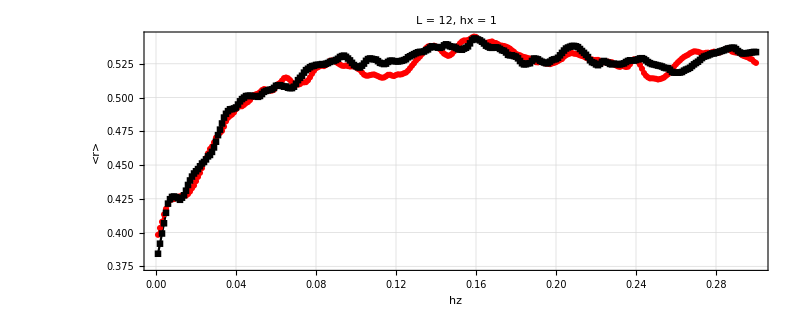

```mathematica
ListPlot[{dataeven,dataodd},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", hx = "<>ToString[hx]<>" ",30,Black],FrameLabel->{Style["hz",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4]
```

```mathematica
J=1;
hz=1;
hxlist=Range[0.01,2,0.01];
hxlist//Length
```

200

```mathematica
Clear[rval];
rval[hx_,hz_]:=Module[{H=IsingNNOpenHamiltonian[hx,hz,J,L],Heven,Hodd,evenval,oddval},
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
evenval=Eigenvalues[Heven];
oddval=Eigenvalues[Hodd];
{hz,MeanLevelSpacingRatio[evenval],MeanLevelSpacingRatio[oddval]}
];
```

```mathematica
data=ParallelTable[Quiet[rval[hx,hz]],{hx,hxlist},DistributedContexts->Full];
```

```mathematica
data=Table[{hxlist[[i]],data[[i,2]],data[[i,3]]},{i,Length[data]}];
```

```mathematica
dataeven=Table[{data[[j,1]],data[[j,2]]},{j,Length[hxlist]}];
dataodd=Table[{data[[j,1]],data[[j,3]]},{j,Length[hxlist]}];
```

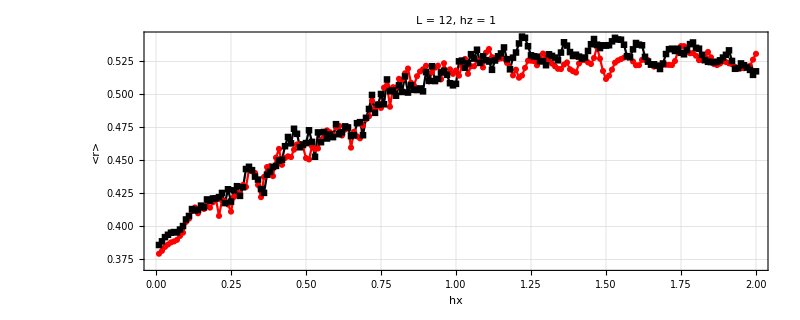

```mathematica
ListPlot[{dataeven,dataodd},PlotRange->All,PlotStyle->{Red,Black},PlotTheme->"Detailed",PlotLabel->Style["L = "<>ToString[L]<>", hz = "<>ToString[hz]<>" ",30,Black],FrameLabel->{Style["hx",25,Black],Style["<r>",25,Black]},ImageSize->800,FrameStyle->Directive[Black,20],Joined->True,PlotMarkers->Automatic,AspectRatio->0.4]
```

# <r> grid

```mathematica
L=11;
```

```mathematica
basis=Tuples[{0,1},L];
ToIndex[state_List]:=FromDigits[state,2]+1;
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,1,Length[basis]}];
permCycles=PermutationCycles[permutation];
R=PermutationMatrix[permCycles,2^L];
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
Beven=Transpose[evenBasis];
Bodd=Transpose[oddBasis];
```

```mathematica
J=0.25;
```

```mathematica
hzlist=Range[0.01,1,0.01];
hxlist=Range[0.1,2,0.1];
Length[hzlist]*Length[hxlist]
```

2000

```mathematica
Clear[rval];
rval[hx_,hz_]:=Module[{H=IsingNNOpenHamiltonian[hx,hz,J,L],Heven,Hodd,evenval,oddval},
Heven=ConjugateTranspose[Beven].H.Beven;
Hodd=ConjugateTranspose[Bodd].H.Bodd;
evenval=Eigenvalues[Heven];
oddval=Eigenvalues[Hodd];
{hx,hz,MeanLevelSpacingRatio[evenval],MeanLevelSpacingRatio[oddval]}
];
```

```mathematica
data=ParallelTable[rval[hx,hz],{hx,hxlist},{hz,hzlist},DistributedContexts->Full];
```

```mathematica
dataeven=Flatten[Table[{data[[i,j,1]],data[[i,j,2]],data[[i,j,3]]},{i,Length[hxlist]},{j,Length[hzlist]}],1];
dataodd=Flatten[Table[{data[[i,j,1]],data[[i,j,2]],data[[i,j,4]]},{i,Length[hxlist]},{j,Length[hzlist]}],1];
```

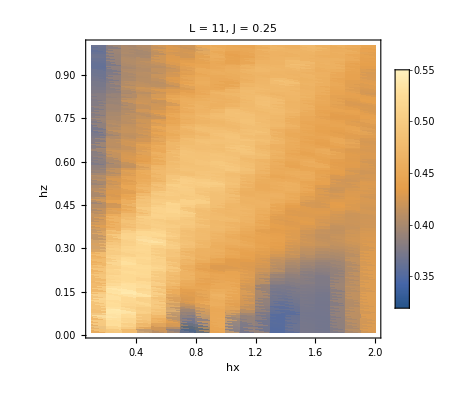

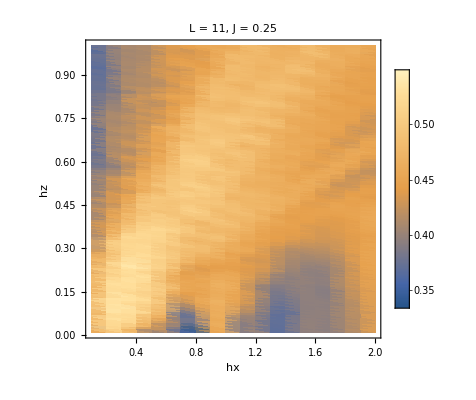

```mathematica
ListDensityPlot[dataeven,PlotTheme->"Detailed",FrameLabel->{Style["hx",20,Black],Style["hz",20,Black]},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J],30,Black]]
ListDensityPlot[dataodd,PlotTheme->"Detailed",FrameLabel->{Style["hx",20,Black],Style["hz",20,Black]},PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J],30,Black]]
```

# Density of states

```mathematica
h=1.0;
g=2.0;
H=IsingNNOpenHamiltonian[h,g,J,L];
transform=Join[evenEigenvectors,oddEigenvectors];
newH=transform.H.ConjugateTranspose[transform];
evenH=newH[[1;;Length[evenEigenvectors],1;;Length[evenEigenvectors]]];
oddH=newH[[Length[evenEigenvectors]+1;;-1,Length[evenEigenvectors]+1;;-1]];
{evenval,evenvec}=Transpose[Sort[Transpose[Eigensystem[evenH]]]];
{oddval,oddvec}=Transpose[Sort[Transpose[Eigensystem[oddH]]]];
```

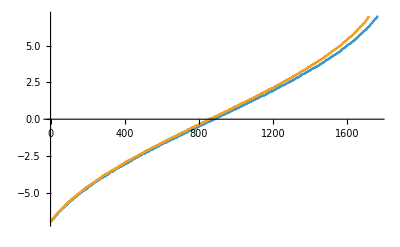

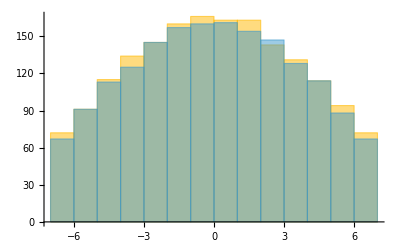

0.427987

0.424896

```mathematica
δ=7;
ListPlot[{Select[evenval,-δ<=#<=δ&],Select[oddval,-δ<=#<=δ&]}]
Histogram[{Select[evenval,-δ<=#<=δ&],Select[oddval,-δ<=#<=δ&]}]
MeanLevelSpacingRatio[Select[evenval,-δ<=#<=δ&]]
MeanLevelSpacingRatio[Select[oddval,-δ<=#<=δ&]]
```

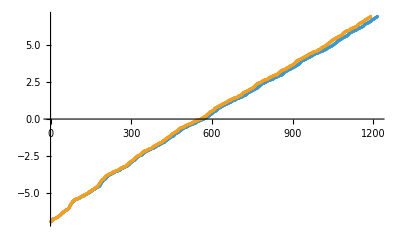

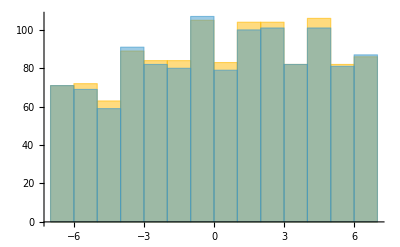

0.416349

0.410082

```mathematica
δ=7;
ListPlot[{Select[evenval,-δ<=#<=δ&],Select[oddval,-δ<=#<=δ&]}]
Histogram[{Select[evenval,-δ<=#<=δ&],Select[oddval,-δ<=#<=δ&]}]
MeanLevelSpacingRatio[Select[evenval,-δ<=#<=δ&]]
MeanLevelSpacingRatio[Select[oddval,-δ<=#<=δ&]]
```

## Spectrum

```mathematica
L=12;
```

```mathematica
J=1;
h=1.;
g=0.5;
H=IsingNNOpenHamiltonian[h,g,J,L];
```

```mathematica
(*Generate the computational basis (list of bit strings)*)
basis=Tuples[{0,1},L];
(*The basis will contain 16 elements,each representing a state|s1,s2,s3,s4>*)
(*Convert a given binary state (list) to an integer index*)
ToIndex[state_List]:=FromDigits[state,2]+1;
(*For each basis state,find the index of its reflection*)
permutation=Table[ToIndex[Reverse[basis[[i]]]],{i,1,Length[basis]}];
(*Convert the mapping into a permutation cycles object*)
permCycles=PermutationCycles[permutation];
(*Construct the reflection symmetry operator as a 16x16 permutation matrix*)
R=PermutationMatrix[permCycles,2^L];
```

```mathematica
{evalR,evecR}=Eigensystem[R];
evenIndices=Flatten[Position[evalR,1]];
oddIndices=Flatten[Position[evalR,-1]];
evenBasis=evecR[[evenIndices]];
oddBasis=evecR[[oddIndices]];
```

```mathematica
(*Form the change-of-basis matrix for the even sector*)
Beven=Transpose[evenBasis];
(*The projected even sector Hamiltonian is then:*)
Heven=ConjugateTranspose[Beven].H.Beven;
(*Similarly for the odd sector*)
Bodd=Transpose[oddBasis];
Hodd=ConjugateTranspose[Bodd].H.Bodd;
```

```mathematica
Peven=ConjugateTranspose[Beven].N[R].Beven;
Podd=ConjugateTranspose[Bodd].R.Bodd;
```

```mathematica
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[Heven]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[Hodd]]]];
```

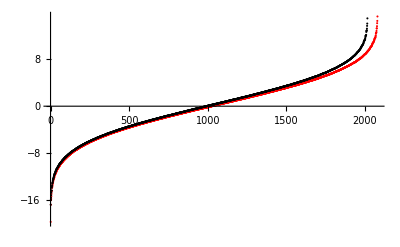

```mathematica
ListPlot[{eveneigenval,oddeigenval},PlotRange->All,PlotStyle->{Red,Black}]
```

```mathematica
MeanLevelSpacingRatio[eveneigenval]
MeanLevelSpacingRatio[oddeigenval]
```

0.526817

0.52442

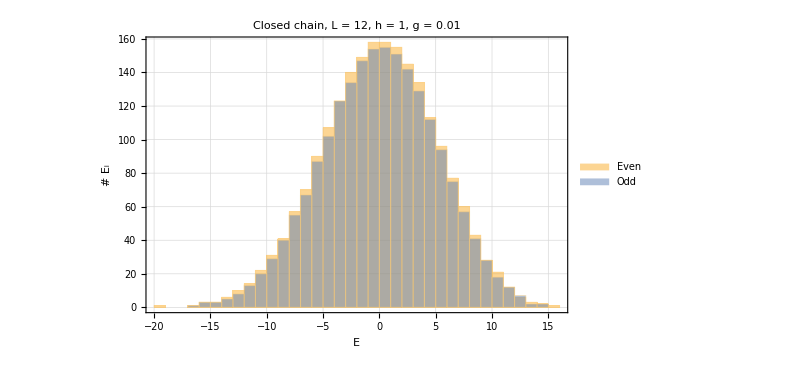

```mathematica
Histogram[{eveneigenval,oddeigenval},PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["Closed chain, L = 12, h = 1, g = 0.01",30,Black],FrameLabel->{Style["E",30,Black],Style["# E_i",30,Black]},FrameStyle->{{25,Black},{25,Black}},ChartLegends->{Style["Even",25,Black],Style["Odd",25,Black]}]
```

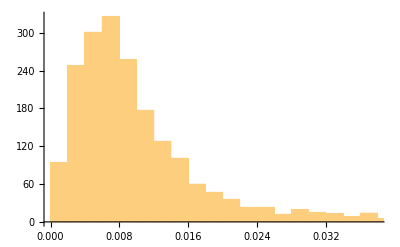

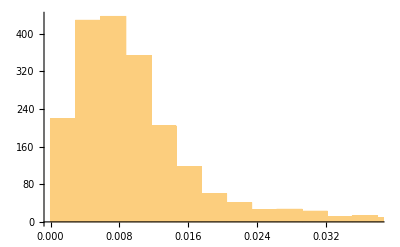

```mathematica
Histogram[Differences[oddeigenval]]
Histogram[Differences[eveneigenval]]
```

```mathematica
evenrelative=Table[(eveneigenval[[i+1]]-eveneigenval[[i]])/(eveneigenval[[i+1]]+eveneigenval[[i]]),{i,Length[eveneigenval]-1}];
```

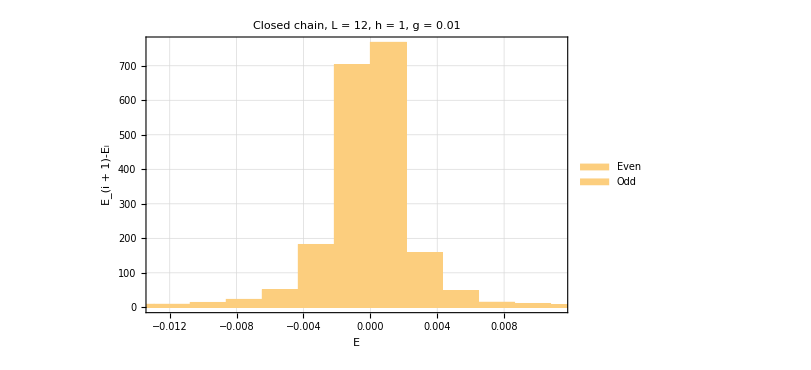

```mathematica
Histogram[evenrelative,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["Closed chain, L = 12, h = 1, g = 0.01",30,Black],FrameLabel->{Style["E",30,Black],Style["E_(i + 1)-E_i",30,Black]},FrameStyle->{{25,Black},{25,Black}},ChartLegends->{Style["Even",25,Black],Style["Odd",25,Black]}]
```

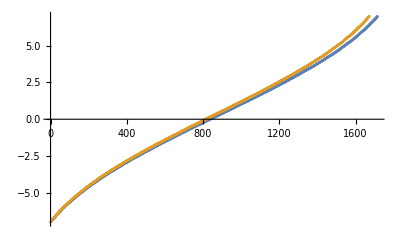

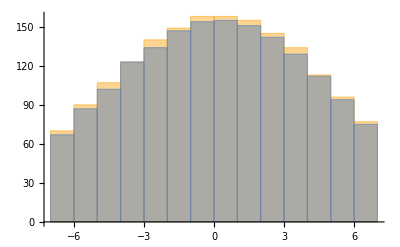

0.525925

0.526574

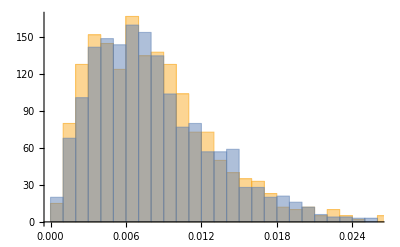

```mathematica
δ=7;
ListPlot[{Select[eveneigenval,-δ<=#<=δ&],Select[oddeigenval,-δ<=#<=δ&]}]
Histogram[{Select[eveneigenval,-δ<=#<=δ&],Select[oddeigenval,-δ<=#<=δ&]}]
MeanLevelSpacingRatio[Select[eveneigenval,-δ<=#<=δ&]]
MeanLevelSpacingRatio[Select[oddeigenval,-δ<=#<=δ&]]
Histogram[{Differences[Select[eveneigenval,-δ<=#<=δ&]],Differences[Select[oddeigenval,-δ<=#<=δ&]]}]
```

```mathematica
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[H]]]];
```

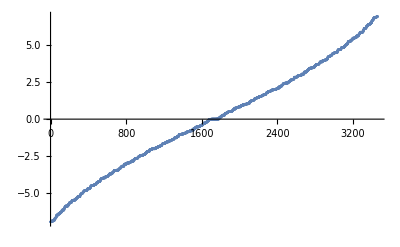

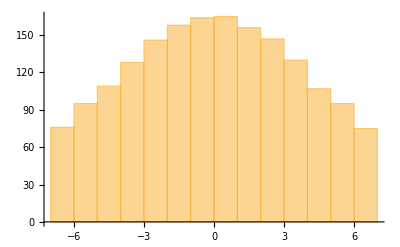

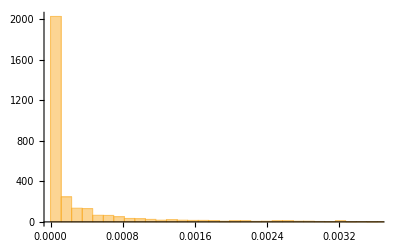

```mathematica
δ=7;
ListPlot[{Select[eigenval,-δ<=#<=δ&]}]
Histogram[{Select[evenval,-δ<=#<=δ&]}]
Histogram[{Differences[Select[eigenval,-δ<=#<=δ&]]}]
```